# Wavelet Proposal

## Haar wavelets

Piecewise[{{-1, 1/2<x<1}, {1, 0<x<1/2}, {0, True}}]

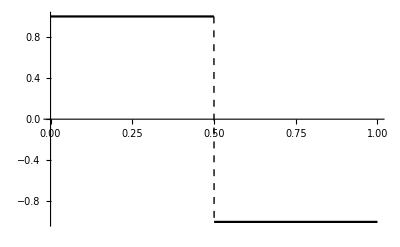

Piecewise[{{-1, 3/2<x<2}, {1, 1<x<3/2}, {0, True}}]

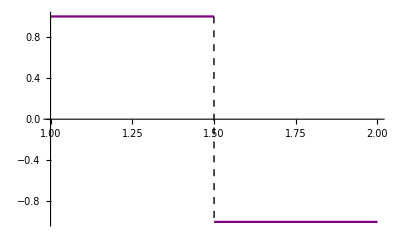

Piecewise[{{-1, 15/16<x<1}, {1, 7/8<x<15/16}, {0, True}}]

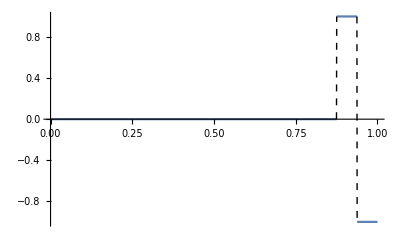

2

12

Piecewise[{{2, 3<x<25/8}, {-2, 25/8<x<13/4}, {0, True}}]

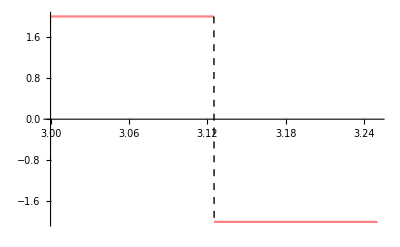

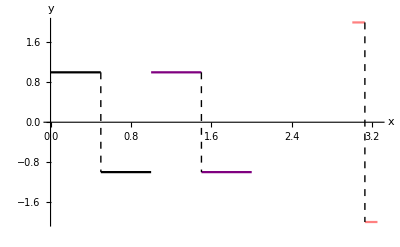

```mathematica
P=Piecewise[{{-1, 1/2<x<1}, {1, 0<x<1/2}}]
p1 = Plot[P,{x,0,1}, ExclusionsStyle->Dashed,PlotStyle->Black]
P01=Piecewise[{{-1, 1+1/2<x<1+1}, {1, 1<x<1+1/2}}]
p01 = Plot[P01,{x,1,2}, ExclusionsStyle->Dashed,PlotStyle->Purple]
P34=Piecewise[{{-1, (1/2+7)/8<x<1}, {1, 7/8<x<(1/2+7)/8}}]
p34 = Plot[P34,{x,0,1}, ExclusionsStyle->Dashed]
j=2
k=12
h=Piecewise[{{2^(j/2), (k/(2^j))<x<(1/2+k)/(2^j)}, {-2^(j/2), (1/2+k)/(2^j)<x<(1+k)/(2^j)}}]
h1 = Plot[h,{x,3,13/4}, ExclusionsStyle->Dashed,PlotLegends->Automatic,PlotStyle->Pink]

plot = Show[p1,p01,h1,PlotRange->All, AxesLabel->{"x","y"}]
```

```mathematica
Blue
```

```mathematica
Legended[plot,LineLegend[{Black,Purple,Pink},{ψ,Subscript[ψ,"0,1"],Subscript[ψ,"2,12"]}]]
```

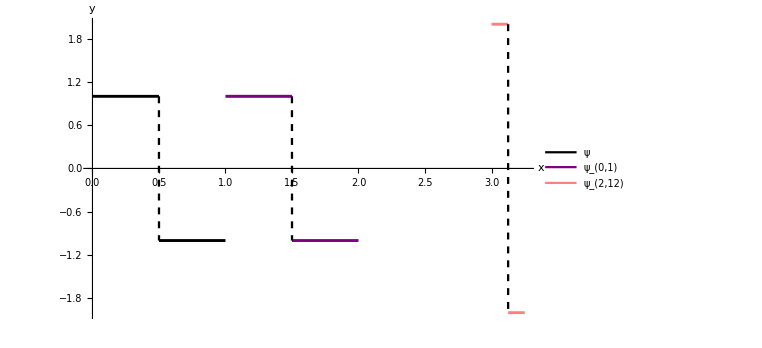

## Example of Function Approximations

```mathematica
f = E^-x Sin[2 Pi x]
```

ⅇ^-x Sin[2 π x]

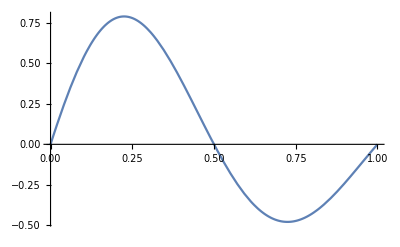

```mathematica
Plot[f,{x,0,1}]
```